## Load the data (sorry, can’t share the raw data)

```mathematica
fileName = FileNameJoin[{Directory[], "Documents","Dropbox","Mathematica Notebooks", "Capers Jones - Benchmarks Interest Levels 2013 v4.xlsx"}];
```

```mathematica
dataFile = Import[fileName][[2]];
```

```mathematica
fieldNames = TableForm[First[dataFile], TableHeadings->{Automatic, None}]
```

1 | Type
2 | ID
3 | Benchmark
4 | Shareholders
5 | CEO
6 | CFO
7 | CIO
8 | CTO
9 | Business Manager
10 | Project Manager
11 | Technical Staff
12 | SQA
13 | Client
14 | Annual Subscription Cost (1,000 Employee Organization)
15 | Number of Benchmark Users (1,000 Employee Organization)
16 | Hours to Collect Data
17 | Cost to Collect Data
18 | Measured by SRM?
19 | Best Metrics for Benchmark

This is the data as we need it.

```mathematica
d = Rest[dataFile];
```

## Benchmark categories

```mathematica
(* **************************** *)
```

```mathematica
(* What are the categories and the benchmarks within each category? *)
```

```mathematica
cats = Tally[d[[All,1]]]
```

{{Business,10},{Delivery,20},{Risk,7},{Process Maturity,11},{Quality,8},{Cost,4}}

```mathematica
(* Data by Categories *)
```

```mathematica
{dBusiness, dDelivery, dRisk, dProcMaturity, dQuality, dCost} = Table[Select[d, #[[1]] == cats[[i]][[1]]&], {i, 1, Length[cats]}];
```

```mathematica
dCost
```

{{Cost,20.,Development costs,8.,10.,10.,10.,10.,8.,8.,7.,7.,10.,1897.37,58.5021,300.,112500.,1.,Function points},{Cost,33.,Enhancement costs,8.,8.,10.,10.,8.,9.,7.,5.,6.,9.,1423.02,20.5548,120.,45000.,1.,Function points},{Cost,34.,Maintenance costs (annual),9.,8.,9.,9.,9.,8.,5.,5.,9.,10.,1423.02,20.5548,300.,112500.,1.,Function points, defect removal},{Cost,39.,Portfolio maintenance costs,10.,10.,10.,10.,10.,10.,7.,5.,4.,4.,4743.42,12.6491,600.,225000.,1.,Function points}}

## Data by benchmark category and audience

```mathematica
(* Data by Business Category by Audience *)
dB={dTypeB, dIDB, dBenchmarkB, dShareholdersB, dCEOB, dCFOB, dCIOB, dCTOB, dBizManB, dProjManB, dTechStaffB, dSQAB, dClientB, dSubscriptionCostB, dUsersB, dDataHoursB, dDataCostB, dSRMAvailB, dMetricB} = Table[dBusiness[[All, i]] , {i, 1,19}];
```

```mathematica
(* Data by Delivery Category by Audience *)
dD = {dTypeD, dIDD, dBenchmarkD, dShareholdersD, dCEOD, dCFOD, dCIOD, dCTOD, dBizManD, dProjManD, dTechStaffD, dSQAD, dClientD, dSubscriptionCostD, dUsersD, dDataHoursD, dDataCostD, dSRMAvailD, dMetricD} = Table[dDelivery[[All, i]] , {i, 1,19}];
```

```mathematica
(* Data by Risk by Audience *)
dR = {dTypeR, dIDR, dBenchmarkR, dShareholdersR, dCEOR, dCFOR, dCIOR, dCTOR, dBizManR, dProjManR, dTechStaffR, dSQAR, dClientR, dSubscriptionCostR, dUsersR, dDataHoursR, dDataCostR, dSRMAvailR, dMetricR} = Table[dRisk[[All, i]] , {i, 1,19}];
```

```mathematica
(* Data by Process Maturity by Audience *)
dP = {dTypeP, dIDP, dBenchmarkP, dShareholdersP, dCEOP, dCFOP, dCIOP, dCTOP, dBizManP, dProjManP, dTechStaffP, dSQAP, dClientP, dSubscriptionCostP, dUsersP, dDataHoursP, dDataCostP, dSRMAvailP, dMetricP} = Table[dProcMaturity[[All, i]] , {i, 1,19}];
```

```mathematica
(* Data by Quality by Audience *)
dQ = {dTypeQ, dIDQ, dBenchmarkQ, dShareholdersQ, dCEOQ, dCFOQ, dCIOQ, dCTOQ, dBizManQ, dProjManQ, dTechStaffQ, dSQAQ, dClientQ, dSubscriptionCostQ, dUsersQ, dDataHoursQ, dDataCostQ, dSRMAvailQ, dMetricQ} = Table[dQuality[[All, i]] , {i, 1,19}];
```

```mathematica
(* Data by Cost by Audience *)
dC = {dTypeC, dIDC, dBenchmarkC, dShareholdersC, dCEOC, dCFOC, dCIOC, dCTOC, dBizManC, dProjManC, dTechStaffC, dSQAC, dClientC, dSubscriptionCostC, dUsersC, dDataHoursC, dDataCostC, dSRMAvailC, dMetricC} = Table[dCost[[All, i]] , {i, 1,19}];
```

```mathematica
dC
```

{{Cost,Cost,Cost,Cost},{20.,33.,34.,39.},{Development costs,Enhancement costs,Maintenance costs (annual),Portfolio maintenance costs},{8.,8.,9.,10.},{10.,8.,8.,10.},{10.,10.,9.,10.},{10.,10.,9.,10.},{10.,8.,9.,10.},{8.,9.,8.,10.},{8.,7.,5.,7.},{7.,5.,5.,5.},{7.,6.,9.,4.},{10.,9.,10.,4.},{1897.37,1423.02,1423.02,4743.42},{58.5021,20.5548,20.5548,12.6491},{300.,120.,300.,600.},{112500.,45000.,112500.,225000.},{1.,1.,1.,1.},{Function points,Function points,Function points, defect removal,Function points}}

```mathematica
dProcMaturity
```

{{Process Maturity,8.,CMMI assessments,8.,9.,9.,9.,10.,9.,9.,10.,10.,10.,3320.39,55.3399,240.,90000.,0.,Key process indicators (KPI)},{Process Maturity,17.,Customer support benchmarks,9.,9.,9.,10.,10.,10.,9.,7.,8.,10.,711.512,22.1359,250.,93750.,0.,Customers served per time unit; customer satisfaction},{Process Maturity,22.,ISO standards certification,8.,9.,9.,9.,9.,9.,9.,8.,8.,10.,2371.71,56.921,120.,45000.,0.,No standard metrics},{Process Maturity,23.,Best Practices - maintenance,8.,8.,9.,10.,10.,8.,8.,7.,7.,10.,4743.42,15.8114,124.,46500.,1.,Function points},{Process Maturity,24.,Best Practices - test efficiency,6.,8.,7.,9.,10.,10.,6.,8.,9.,10.,1897.37,11.8585,140.,52500.,1.,Function points, defect removal},{Process Maturity,25.,Best Practices - defect prevention,6.,5.,6.,8.,10.,9.,9.,9.,9.,10.,1423.02,10.4355,200.,75000.,1.,Function points, defect prevention},{Process Maturity,26.,Best Practices - pre-test defects,5.,6.,6.,9.,10.,9.,9.,8.,9.,9.,1897.37,7.90569,240.,90000.,1.,Function points, defect removal},{Process Maturity,37.,Best Practices - design,4.,5.,5.,9.,10.,8.,7.,9.,9.,9.,1897.37,14.2302,140.,52500.,1.,Function points},{Process Maturity,50.,CMMI levels within industries,4.,6.,5.,5.,9.,7.,7.,4.,8.,6.,474.342,60.0833,120.,45000.,1.,Percentage by CMMI levels},{Process Maturity,51.,Standards benchmarks,3.,5.,5.,6.,8.,8.,6.,5.,4.,10.,474.342,3.16228,90.,33750.,0.,Function points, defect removal},{Process Maturity,55.,Metrics used,3.,3.,3.,7.,9.,9.,7.,3.,7.,5.,474.342,31.6228,90.,33750.,1.,Percentage by metric}}

```mathematica
(* Data by Audience Across all Categories *)
```

```mathematica
dByField={dType, dID, dBenchmark, dShareholders, dCEO, dCFO, dCIO, dCTO, dBizMan, dProjMan, dTechStaff, dSQA, dClient, dSubscriptionCost, dUsers, dDataHours, dDataCost, dSRMAvail, dMetric} = Table[d[[All, i]] , {i, 1,19}];
```

```mathematica
(* Audience Names *)
audiences = {"Sholders", "CEO", "CFO", "CIO", "CTO", "BizMan", "ProjMan", "TechStaff", "SQA", "Client"};
```

```mathematica
dBenchmark;
```

```mathematica
dCEO
```

{10.,10.,10.,10.,10.,9.,10.,9.,10.,9.,10.,9.,10.,10.,10.,10.,9.,10.,6.,10.,7.,9.,8.,8.,5.,6.,8.,8.,7.,7.,6.,8.,8.,8.,8.,10.,5.,10.,10.,10.,10.,5.,5.,5.,4.,2.,7.,7.,4.,6.,5.,8.,9.,10.,3.,3.,4.,3.,1.,3.}

```mathematica
dShareholders
```

{10.,10.,10.,9.,10.,8.,10.,8.,10.,9.,10.,8.,10.,10.,9.,8.,9.,9.,5.,8.,5.,8.,8.,6.,6.,5.,6.,8.,6.,6.,6.,5.,8.,9.,8.,10.,4.,10.,10.,10.,10.,4.,9.,6.,6.,2.,6.,5.,4.,4.,3.,6.,9.,7.,3.,2.,4.,2.,1.,2.}

```mathematica
corrTable[headings_, data_]:= Module[{c,t},
c = Correlation[Transpose[data]];
t =Column[{GraphicsRow[headings,ImageSize->500,Frame->All],Row[{GraphicsColumn[headings,ImageSize->50,Frame->All],Overlay[{ArrayPlot[c,ColorFunction->(ColorData["TemperatureMap"][(1+#)/2]&),Frame->None,Mesh->True,PlotRangePadding->0,ImageSize->500,ColorFunctionScaling->False],GraphicsGrid[Map[NumberForm[#,2]&,c,{2}],ImageSize->500]}]}]},Alignment->Right,Spacings->0]
]
```

```mathematica
(* (Q1) In general, over all the benchmarks across all the categories, which audiences are the most similar? Which audiences are the most dissimilar? *)
```

```mathematica
(* Create a correlation table - Mathematica Document: example/CreateACorrelationTable *)
```

```mathematica
t = {dShareholders,dCEO, dCFO, dCIO, dCTO, dBizMan, dProjMan, dTechStaff, dSQA, dClient};
```

```mathematica
Transpose[t];
```

```mathematica
t2 = Correlation[Transpose[t]];
```

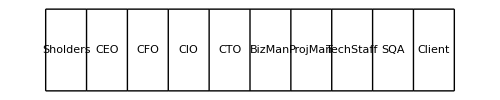
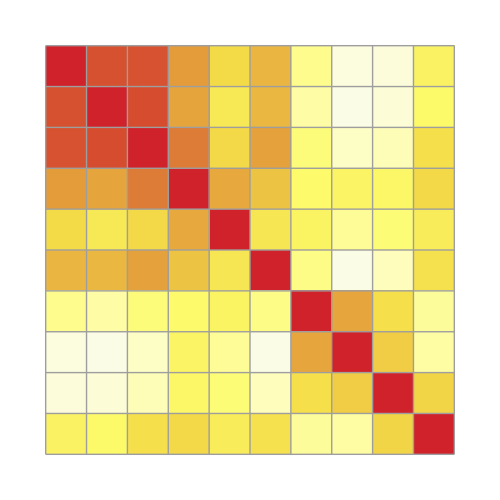
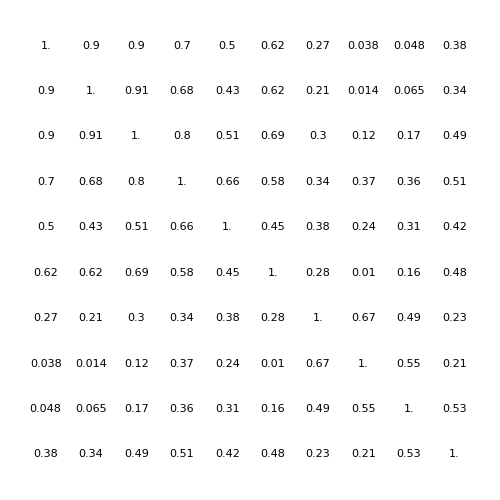
-Graphics-
-Graphics--Graphics--Graphics-

```mathematica
Column[{GraphicsRow[audiences,ImageSize->500,Frame->All],Row[{GraphicsColumn[audiences,ImageSize->50,Frame->All],Overlay[{ArrayPlot[t2,ColorFunction->(ColorData["TemperatureMap"][(1+#)/2]&),Frame->None,Mesh->True,PlotRangePadding->0,ImageSize->500,ColorFunctionScaling->False],GraphicsGrid[Map[NumberForm[#,2]&,t2,{2}],ImageSize->500]}]}]},Alignment->Right,Spacings->0]
```

{Competitive practices within industry,Attrition by role & size & industry,Compensation by Role,Roles by industry & size,Return on investment (ROI),Skills inventories by role,Total cost of ownership (TCO),Customer satisfaction,Employee morale,Industry productivity}

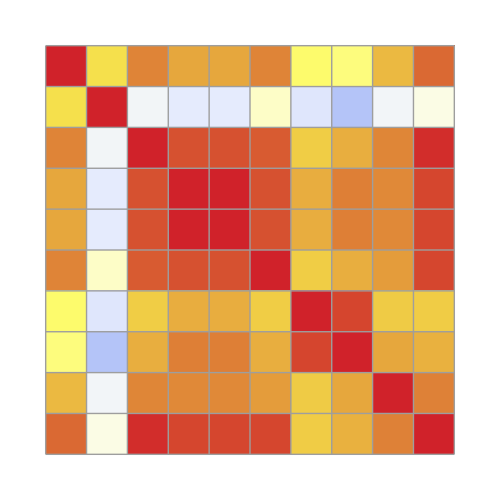
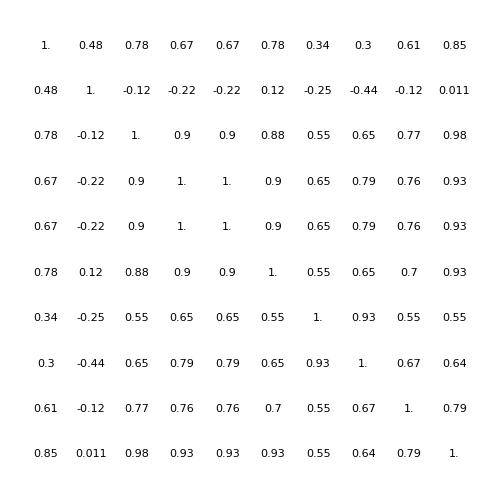
-Graphics-
-Graphics--Graphics--Graphics-

```mathematica
(* Q2 - for the metrics in the Business category, how similar or dissimilar are the various audiences? *)
benchmarksB = dBusiness[[All, 3]]
corrTable[audiences, Take[dB, {4,13}]]
```

{Project failure rates (size, methods),Development Schedules,Outsource contract success/failure,Best Practices - requirements,Team attrition rates,Productivity - project,Coding speed,Application sizes by type,Team morale,Team compensation level,Earned value (EVA),Delivery methodology comparisons,Productivity - activity based,Application types,Tool suites used,Country productivity,Database size,Programming Languages,Application class by taxonomy ,SNAP non functional size metrics}

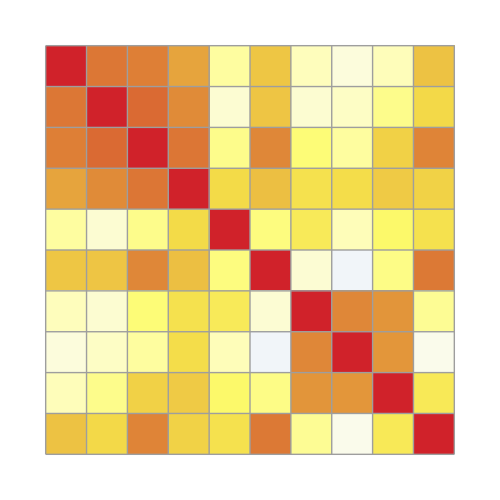
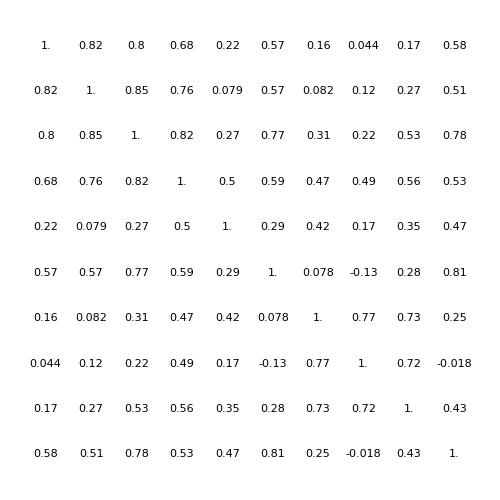
-Graphics-
-Graphics--Graphics--Graphics-

```mathematica
(* Q3 - for the metrics in the Delivery category, how similar or dissimilar are the various audiences? *)
benchmarksD = dDelivery[[All, 3]]
corrTable[audiences, Take[dD, {4,13}]]
```

{Project Risks,Security attacks (number & type),Technical debt,Litigation - patent infringements,Litigation - intellectual property,Litigation - breach of contract,Litigation - employment contracts}

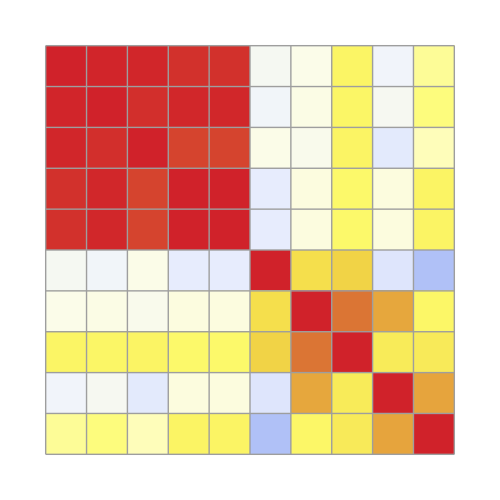
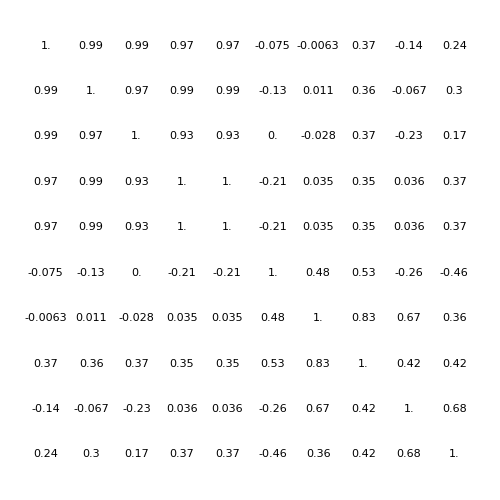
-Graphics-
-Graphics--Graphics--Graphics-

```mathematica
(* Q4 - for the metrics in the Risk category, how similar or dissimilar are the various audiences? *)
benchmarksR = dRisk[[All, 3]]
corrTable[audiences, Take[dR, {4,13}]]
```

{CMMI assessments,Customer support benchmarks,ISO standards certification,Best Practices - maintenance,Best Practices - test efficiency,Best Practices - defect prevention,Best Practices - pre-test defects,Best Practices - design,CMMI levels within industries,Standards benchmarks,Metrics used}

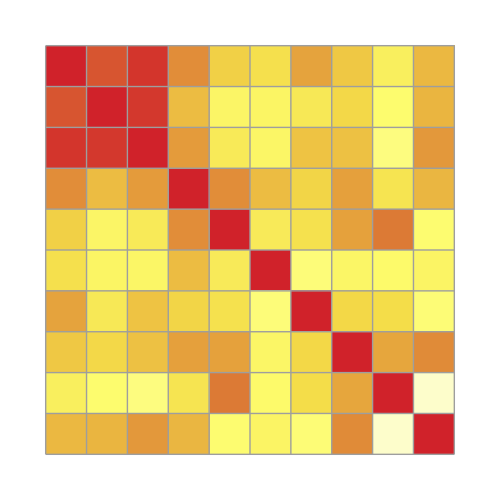
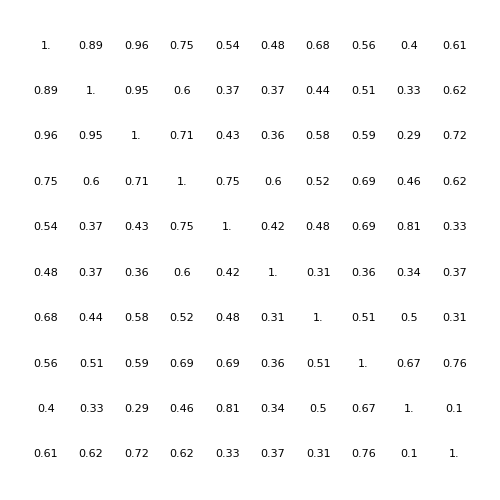
-Graphics-
-Graphics--Graphics--Graphics-

```mathematica
(* Q5 - for the metrics in the Process Maturity category, how similar or dissimilar are the various audiences? *)
benchmarksP = dProcMaturity[[All, 3]]
corrTable[audiences, Take[dP, {4,13}]]
```

{Data quality,Cost of Quality (COQ)/technical debt,Code quality (only code - nothing else),Cost per defect (caution: unreliable),Test coverage benchmarks,Serviceability benchmarks,Certification benchmarks,Cyclomatic complexity benchmarks}

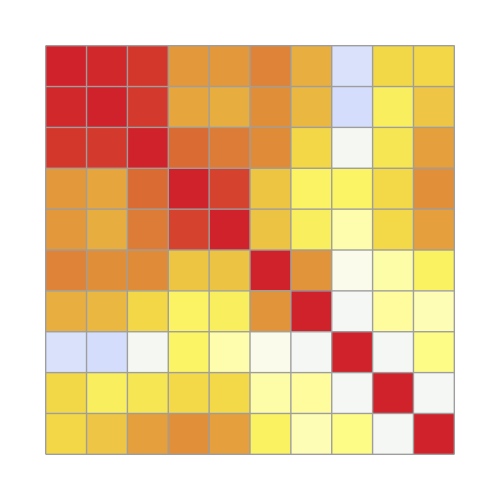
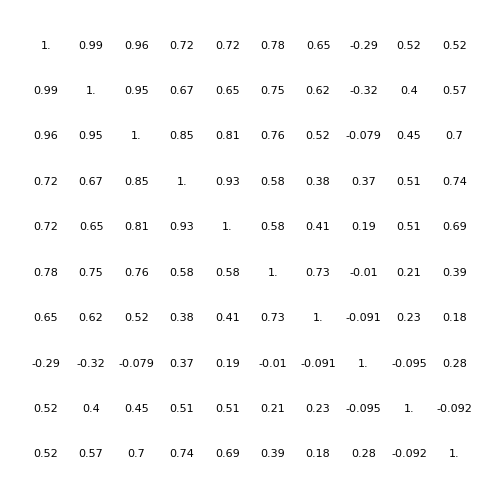
-Graphics-
-Graphics--Graphics--Graphics-

```mathematica
(* Q6 - for the metrics in the Quality category, how similar or dissimilar are the various audiences? *)
benchmarksQ = dQuality[[All, 3]]
corrTable[audiences, Take[dQ, {4,13}]]
```

{Development costs,Enhancement costs,Maintenance costs (annual),Portfolio maintenance costs}

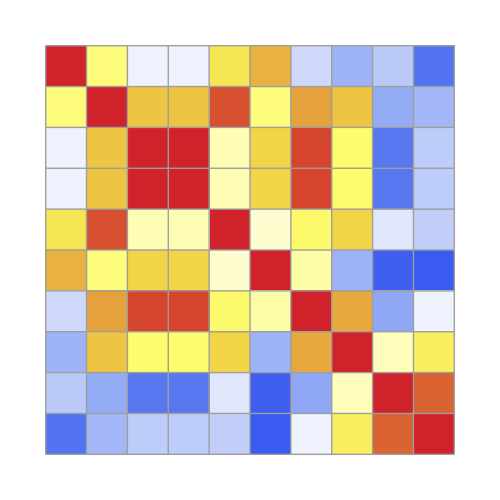
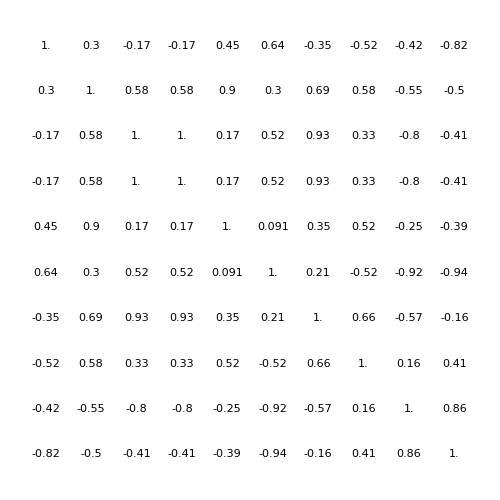
-Graphics-
-Graphics--Graphics--Graphics-

```mathematica
(* Q7 - for the metrics in the Cost category, how similar or dissimilar are the various audiences? *)
benchmarksC = dCost[[All, 3]]
corrTable[audiences, Take[dC, {4,13}]]
```

We now know how the various stakeholders are aligned (or not) with each other in terms of their inteterests. What we don’t know yet is whether they are aligned because they are both interested in something or whether they are not interested in something.

## Pairwise comparisons of stakeholders’ interests

Let's study what exactly the levels of interest or disinterest are. There are 90 pairs of stakeholders that can be compared. Let's look at some key comparisons. For each stakeholder, we’ll segment the benchmarks according to “Interesting”, “Somewhat Interesting”, and “Not Interesting”. To creat this segmentation, we’ll set up thresholds for the benchmark values. In particular, we’ll set:

```mathematica
interestLevelMap = Association[{1. -> "Not Interesting",2. -> "Not Interesting",3. -> "Not Interesting",4. -> "Not Interesting",  5. -> "Somewhat Interesting", 6. -> "Somewhat Interesting", 7. -> "Somewhat Interesting",  8. -> "Interesting",9. -> "Interesting",10. -> "Interesting"}]
```

<|1.→Not Interesting,2.→Not Interesting,3.→Not Interesting,4.→Not Interesting,5.→Somewhat Interesting,6.→Somewhat Interesting,7.→Somewhat Interesting,8.→Interesting,9.→Interesting,10.→Interesting|>

```mathematica
interestLevels = {"Interesting", "Somewhat Interesting", "Not Interesting"};
```

```mathematica
interestPatterns = Tuples[{interestLevels, interestLevels}]
```

{{Interesting,Interesting},{Interesting,Somewhat Interesting},{Interesting,Not Interesting},{Somewhat Interesting,Interesting},{Somewhat Interesting,Somewhat Interesting},{Somewhat Interesting,Not Interesting},{Not Interesting,Interesting},{Not Interesting,Somewhat Interesting},{Not Interesting,Not Interesting}}

```mathematica
interestPatterns
```

{{Interesting,Interesting},{Interesting,Somewhat Interesting},{Interesting,Not Interesting},{Somewhat Interesting,Interesting},{Somewhat Interesting,Somewhat Interesting},{Somewhat Interesting,Not Interesting},{Not Interesting,Interesting},{Not Interesting,Somewhat Interesting},{Not Interesting,Not Interesting}}

```mathematica
Length[interestPatterns]
```

9

```mathematica
TableForm[interestPatterns, TableHeadings->{Automatic, {"Stakeholder 1", "Stakeholder 2"}}]
```

| Stakeholder 1 | Stakeholder 2
1 | Interesting | Interesting
2 | Interesting | Somewhat Interesting
3 | Interesting | Not Interesting
4 | Somewhat Interesting | Interesting
5 | Somewhat Interesting | Somewhat Interesting
6 | Somewhat Interesting | Not Interesting
7 | Not Interesting | Interesting
8 | Not Interesting | Somewhat Interesting
9 | Not Interesting | Not Interesting

```mathematica
benchmarkTypes = cats[[All,1]]
```

{Business,Delivery,Risk,Process Maturity,Quality,Cost}

```mathematica
dColumnNumbers = Association[{"Benchmark Type" ->  1, "Benchmark Name" ->  3, "Shareholders" ->  4, "CEO" ->  5, "CFO" ->  6, "CIO" ->  7, "CTO" ->  8, "Biz Mgr" ->  9, "Proj Mgr" -> 10, "Tech Staff" ->  11, "SQA" ->  12, "Clients" ->  13}]
```

<|Benchmark Type→1,Benchmark Name→3,Shareholders→4,CEO→5,CFO→6,CIO→7,CTO→8,Biz Mgr→9,Proj Mgr→10,Tech Staff→11,SQA→12,Clients→13|>

```mathematica
dColumnNumbers["CEO"]
```

5

## Comparison of CEOs with CIOs

```mathematica
benchmarkTypeColumn = 1;
benchmarkColumn = 3;
ceoColumn = 5;
cioColumn = 7;
```

Get all the benchmark interest values for CEOs and CIOs segregated into 9 groups depending on what’s interesting, somewhat interesting, and not interesting.

```mathematica
compCEOandCIO = ReplacePart[#, {3 -> Lookup[interestLevelMap,#[[3]]], 4-> Lookup[interestLevelMap, #[[4]]]}] & /@ d[[All, {benchmarkTypeColumn, benchmarkColumn, ceoColumn, cioColumn}]];
```

```mathematica
scompCEOandCIO = Table[GatherBy[Select[compCEOandCIO, #[[3]] == interestPatterns[[i,1]] && #[[4]] == interestPatterns[[i,2]] &], First], {i,1,Length[interestPatterns]}];
```

```mathematica
Table[Quiet[Check[scompCEOandCIO[[i,j]],{}]], {i,1,Length[interestPatterns]},{j,1,Length[benchmarkTypes]}][[1,1]]
```

{{Business,Competitive practices within industry,Interesting,Interesting},{Business,Attrition by role & size & industry,Interesting,Interesting},{Business,Compensation by Role,Interesting,Interesting},{Business,Roles by industry & size,Interesting,Interesting},{Business,Return on investment (ROI),Interesting,Interesting},{Business,Skills inventories by role,Interesting,Interesting},{Business,Total cost of ownership (TCO),Interesting,Interesting},{Business,Customer satisfaction,Interesting,Interesting},{Business,Employee morale,Interesting,Interesting}}

```mathematica
Table[TableForm[Table[TableForm[Flatten[#] & /@ Quiet[Check[scompCEOandCIO[[i,j]],{}]]], {i,1,Length[interestPatterns]},{j,1,Length[benchmarkTypes]}][[k]]], {k, 1, Length[benchmarkTypes]}]
```

{Business | Competitive practices within industry | Interesting | Interesting
Business | Attrition by role & size & industry | Interesting | Interesting
Business | Compensation by Role | Interesting | Interesting
Business | Roles by industry & size | Interesting | Interesting
Business | Return on investment (ROI) | Interesting | Interesting
Business | Skills inventories by role | Interesting | Interesting
Business | Total cost of ownership (TCO) | Interesting | Interesting
Business | Customer satisfaction | Interesting | Interesting
Business | Employee morale | Interesting | Interesting
Delivery | Project failure rates (size, methods) | Interesting | Interesting
Delivery | Development Schedules | Interesting | Interesting
Delivery | Outsource contract success/failure | Interesting | Interesting
Delivery | Productivity - project | Interesting | Interesting
Delivery | Application sizes by type | Interesting | Interesting
Delivery | Team morale | Interesting | Interesting
Delivery | Team compensation level | Interesting | Interesting
Delivery | Country productivity | Interesting | Interesting
Delivery | Database size | Interesting | Interesting
Risk | Project Risks | Interesting | Interesting
Risk | Security attacks (number & type) | Interesting | Interesting
Risk | Technical debt | Interesting | Interesting
Risk | Litigation - patent infringements | Interesting | Interesting
Risk | Litigation - intellectual property | Interesting | Interesting
Risk | Litigation - breach of contract | Interesting | Interesting
Process Maturity | CMMI assessments | Interesting | Interesting
Process Maturity | Customer support benchmarks | Interesting | Interesting
Process Maturity | ISO standards certification | Interesting | Interesting
Process Maturity | Best Practices - maintenance | Interesting | Interesting
Process Maturity | Best Practices - test efficiency | Interesting | Interesting
Quality | Data quality | Interesting | Interesting
Quality | Cost of Quality (COQ)/technical debt | Interesting | Interesting
Cost | Development costs | Interesting | Interesting
Cost | Enhancement costs | Interesting | Interesting
Cost | Maintenance costs (annual) | Interesting | Interesting
Cost | Portfolio maintenance costs | Interesting | Interesting,Business | Industry productivity | Interesting | Somewhat Interesting
{}
{}
{}
{}
{},{}
{}
{}
{}
{}
{},Delivery | Best Practices - requirements | Somewhat Interesting | Interesting
Delivery | Team attrition rates | Somewhat Interesting | Interesting
Delivery | Coding speed | Somewhat Interesting | Interesting
Delivery | Delivery methodology comparisons | Somewhat Interesting | Interesting
Process Maturity | Best Practices - defect prevention | Somewhat Interesting | Interesting
Process Maturity | Best Practices - pre-test defects | Somewhat Interesting | Interesting
Process Maturity | Best Practices - design | Somewhat Interesting | Interesting
Quality | Code quality (only code - nothing else) | Somewhat Interesting | Interesting
Quality | Cost per defect (caution: unreliable) | Somewhat Interesting | Interesting
Quality | Test coverage benchmarks | Somewhat Interesting | Interesting
Risk | Litigation - employment contracts | Somewhat Interesting | Interesting
{}
{},Delivery | Earned value (EVA) | Somewhat Interesting | Somewhat Interesting
Delivery | Application types | Somewhat Interesting | Somewhat Interesting
Process Maturity | CMMI levels within industries | Somewhat Interesting | Somewhat Interesting
Process Maturity | Standards benchmarks | Somewhat Interesting | Somewhat Interesting
{}
{}
{}
{},{}
{}
{}
{}
{}
{}}

## A function for generating the comparisons

```mathematica
getInterestLevelComparisons[ stakeholder1_, stakeholder2_, type_:1, name_:3]:= Module[{compS1andS2, segCompS1andS2, rawTable, rawTableDisplay},
(* type is the column number of the benchmark type in the data file *)
(* name is the column number of the benchmark name in the data file *)
(* stakeholder1 and stakeholder2 are names of stakeholders from the stakeholderNames list above *)
(* Stakeholder names can be "Shareholders", "CEO", "CFO", "CIO", "CTO", "Biz Mgr", "Proj Mgr", "Tech Staff", "SQA", "Clients" *)

(* Get all the results for the two stakeholders in question *)
compS1andS2 = ReplacePart[#, {3 -> Lookup[interestLevelMap,#[[3]]], 4-> Lookup[interestLevelMap, #[[4]]]}] & /@ d[[All, {type, name, dColumnNumbers[stakeholder1], dColumnNumbers[stakeholder2]}]];

(* Segment the data by interest patterns and by benchmark type *)
segCompS1andS2 = Table[GatherBy[Select[compS1andS2, #[[3]] == interestPatterns[[i,1]] && #[[4]] == interestPatterns[[i,2]] &], First], {i,1,Length[interestPatterns]}];

(* Output the raw results *)
rawTable = Table[TableForm[Table[TableForm[Flatten[#] & /@ Quiet[Check[segCompS1andS2[[i,j]],{}]]], {i,1,Length[interestPatterns]},{j,1,Length[benchmarkTypes]}][[k]]], {k, 1, Length[benchmarkTypes]}] ;

(* Remove the empty lists from rawTable *)
rawTableDisplay =  rawTable //.  TableForm[List[]] -> Sequence[]

];
```

```mathematica
getInterestLevelComparisons["CFO","CIO"]
```

{Business | Competitive practices within industry | Interesting | Interesting
Business | Attrition by role & size & industry | Interesting | Interesting
Business | Compensation by Role | Interesting | Interesting
Business | Roles by industry & size | Interesting | Interesting
Business | Return on investment (ROI) | Interesting | Interesting
Business | Skills inventories by role | Interesting | Interesting
Business | Total cost of ownership (TCO) | Interesting | Interesting
Business | Customer satisfaction | Interesting | Interesting
Business | Employee morale | Interesting | Interesting
Delivery | Project failure rates (size, methods) | Interesting | Interesting
Delivery | Development Schedules | Interesting | Interesting
Delivery | Outsource contract success/failure | Interesting | Interesting
Delivery | Best Practices - requirements | Interesting | Interesting
Delivery | Team attrition rates | Interesting | Interesting
Delivery | Productivity - project | Interesting | Interesting
Delivery | Coding speed | Interesting | Interesting
Delivery | Application sizes by type | Interesting | Interesting
Delivery | Team morale | Interesting | Interesting
Delivery | Team compensation level | Interesting | Interesting
Delivery | Database size | Interesting | Interesting
Risk | Project Risks | Interesting | Interesting
Risk | Security attacks (number & type) | Interesting | Interesting
Risk | Technical debt | Interesting | Interesting
Risk | Litigation - patent infringements | Interesting | Interesting
Risk | Litigation - intellectual property | Interesting | Interesting
Risk | Litigation - breach of contract | Interesting | Interesting
Risk | Litigation - employment contracts | Interesting | Interesting
Process Maturity | CMMI assessments | Interesting | Interesting
Process Maturity | Customer support benchmarks | Interesting | Interesting
Process Maturity | ISO standards certification | Interesting | Interesting
Process Maturity | Best Practices - maintenance | Interesting | Interesting
Quality | Data quality | Interesting | Interesting
Quality | Cost of Quality (COQ)/technical debt | Interesting | Interesting
Cost | Development costs | Interesting | Interesting
Cost | Enhancement costs | Interesting | Interesting
Cost | Maintenance costs (annual) | Interesting | Interesting
Cost | Portfolio maintenance costs | Interesting | Interesting,Process Maturity | Best Practices - test efficiency | Somewhat Interesting | Interesting
Process Maturity | Best Practices - defect prevention | Somewhat Interesting | Interesting
Process Maturity | Best Practices - pre-test defects | Somewhat Interesting | Interesting
Process Maturity | Best Practices - design | Somewhat Interesting | Interesting
Quality | Code quality (only code - nothing else) | Somewhat Interesting | Interesting
Quality | Cost per defect (caution: unreliable) | Somewhat Interesting | Interesting
Quality | Test coverage benchmarks | Somewhat Interesting | Interesting
Quality | Serviceability benchmarks | Somewhat Interesting | Interesting
Delivery | Delivery methodology comparisons | Somewhat Interesting | Interesting
Delivery | Productivity - activity based | Somewhat Interesting | Interesting
Delivery | Country productivity | Somewhat Interesting | Interesting,Delivery | Earned value (EVA) | Somewhat Interesting | Somewhat Interesting
Delivery | Application types | Somewhat Interesting | Somewhat Interesting
Delivery | Application class by taxonomy  | Somewhat Interesting | Somewhat Interesting
Process Maturity | CMMI levels within industries | Somewhat Interesting | Somewhat Interesting
Process Maturity | Standards benchmarks | Somewhat Interesting | Somewhat Interesting
Business | Industry productivity | Somewhat Interesting | Somewhat Interesting}

## The Euclidean distance between stakeholders’ interest levels

Let’s see how the participants cluster. This gives us a sense of how similar any two stakeholders are across all their benchmark interest levels.

```mathematica
interestLevelByStakeholder = Transpose[d[[All, 4;;13]]]
```

{{10.,10.,10.,9.,10.,8.,10.,8.,10.,9.,10.,8.,10.,10.,9.,8.,9.,9.,5.,8.,5.,8.,8.,6.,6.,5.,6.,8.,6.,6.,6.,5.,8.,9.,8.,10.,4.,10.,10.,10.,10.,4.,9.,6.,6.,2.,6.,5.,4.,4.,3.,6.,9.,7.,3.,2.,4.,2.,1.,2.},{10.,10.,10.,10.,10.,9.,10.,9.,10.,9.,10.,9.,10.,10.,10.,10.,9.,10.,6.,10.,7.,9.,8.,8.,5.,6.,8.,8.,7.,7.,6.,8.,8.,8.,8.,10.,5.,10.,10.,10.,10.,5.,5.,5.,4.,2.,7.,7.,4.,6.,5.,8.,9.,10.,3.,3.,4.,3.,1.,3.},{10.,10.,10.,10.,10.,10.,10.,9.,10.,10.,10.,9.,10.,10.,9.,10.,9.,10.,9.,10.,8.,9.,9.,7.,6.,6.,8.,8.,8.,7.,7.,8.,10.,9.,8.,10.,5.,10.,10.,9.,10.,6.,7.,6.,6.,5.,7.,8.,4.,5.,5.,5.,8.,7.,3.,3.,5.,3.,1.,4.},{10.,10.,10.,10.,10.,10.,10.,9.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,9.,10.,10.,9.,10.,9.,8.,9.,9.,9.,8.,10.,10.,8.,10.,9.,8.,10.,9.,10.,10.,9.,10.,9.,7.,9.,8.,10.,7.,8.,7.,5.,6.,8.,8.,6.,7.,6.,6.,6.,5.,5.},{10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,9.,10.,10.,10.,10.,9.,10.,8.,10.,10.,9.,8.,9.,8.,10.,10.,10.,10.,7.,10.,8.,10.,10.,10.,10.,9.,8.,10.,9.,8.,9.,9.,9.,9.,8.,8.,7.,7.,8.},{10.,10.,10.,10.,10.,10.,10.,9.,9.,9.,10.,9.,10.,10.,10.,10.,10.,10.,10.,8.,10.,9.,8.,10.,9.,9.,8.,9.,9.,7.,8.,7.,9.,8.,8.,8.,8.,10.,10.,7.,8.,8.,9.,6.,7.,6.,6.,10.,4.,7.,8.,7.,10.,7.,9.,5.,8.,3.,7.,7.},{10.,10.,10.,10.,10.,9.,10.,9.,9.,9.,9.,9.,7.,7.,9.,8.,9.,7.,8.,8.,10.,9.,8.,6.,9.,9.,8.,8.,9.,8.,8.,10.,7.,5.,8.,5.,7.,7.,7.,8.,6.,7.,10.,10.,10.,5.,6.,7.,8.,7.,6.,6.,2.,6.,7.,8.,4.,5.,7.,7.},{10.,10.,10.,10.,9.,10.,8.,10.,8.,9.,8.,10.,6.,7.,9.,7.,7.,6.,9.,7.,10.,8.,7.,8.,9.,8.,5.,8.,9.,8.,8.,8.,5.,5.,10.,5.,9.,6.,5.,10.,4.,10.,5.,10.,9.,10.,6.,5.,10.,4.,5.,6.,1.,3.,3.,10.,4.,6.,7.,5.},{10.,10.,9.,8.,9.,8.,7.,10.,9.,8.,6.,8.,9.,8.,7.,7.,8.,10.,9.,7.,8.,8.,7.,9.,9.,9.,10.,6.,9.,9.,10.,8.,6.,9.,8.,4.,9.,4.,4.,5.,5.,8.,5.,7.,7.,8.,7.,4.,6.,8.,4.,4.,1.,4.,7.,5.,5.,8.,7.,4.},{10.,10.,10.,10.,10.,9.,10.,10.,10.,9.,10.,8.,10.,10.,8.,10.,10.,8.,10.,10.,7.,10.,10.,10.,10.,9.,10.,9.,8.,9.,7.,7.,9.,10.,6.,10.,9.,4.,4.,5.,6.,8.,10.,5.,4.,9.,6.,4.,5.,6.,10.,3.,8.,3.,5.,3.,6.,7.,6.,5.}}

```mathematica
Length[interestLevelByStakeholder]
```

10

The goal is to take the Euclidean distance between each of the lists above with every other list in order. So we have the Euclidean distances for Shareholders with Shareholders, Shareholders with CEOs, Shareholders with CFOs, and so on. Then on to the distance between CEOs and the rest of each of the stakeholders.

```mathematica
simTable = Table[EuclideanDistance[interestLevelByStakeholder[[i]], interestLevelByStakeholder[[j]]], {i, 1, Length[interestLevelByStakeholder]}, {j, 1, Length[interestLevelByStakeholder]}]
```

{{0.,9.69536,10.583,20.,25.7294,19.5448,22.,26.4386,25.0799,22.383},{9.69536,0.,8.12404,17.2627,22.8035,16.9706,21.3073,26.0192,24.3516,21.6102},{10.583,8.12404,0.,13.4164,20.0499,14.0712,18.8149,23.6008,22.1133,18.1384},{20.,17.2627,13.4164,0.,10.198,11.4018,16.3707,20.025,19.9249,16.8226},{25.7294,22.8035,20.0499,10.198,0.,13.3417,17.6068,23.0434,22.6495,19.8242},{19.5448,16.9706,14.0712,11.4018,13.3417,0.,16.3707,22.8254,20.8087,16.6433},{22.,21.3073,18.8149,16.3707,17.6068,16.3707,0.,13.3041,15.5242,19.5704},{26.4386,26.0192,23.6008,20.025,23.0434,22.8254,13.3041,0.,15.8745,22.4054},{25.0799,24.3516,22.1133,19.9249,22.6495,20.8087,15.5242,15.8745,0.,17.2627},{22.383,21.6102,18.1384,16.8226,19.8242,16.6433,19.5704,22.4054,17.2627,0.}}

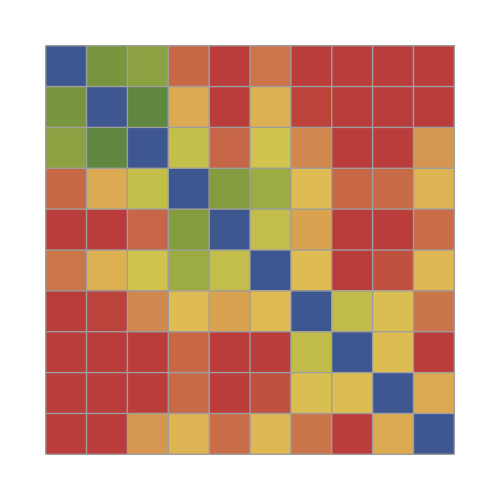
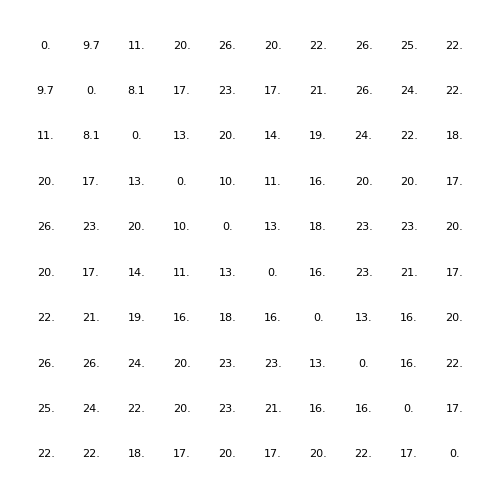
-Graphics-
-Graphics--Graphics--Graphics-

```mathematica
mdTable = Column[{GraphicsRow[audiences,ImageSize->500,Frame->All],Row[{GraphicsColumn[audiences,ImageSize->50,Frame->All],Overlay[{ArrayPlot[simTable,ColorFunction->(ColorData["DarkRainbow"][(1+#)/25]&),Frame->None,Mesh->True,PlotRangePadding->0,ImageSize->500,ColorFunctionScaling->False],GraphicsGrid[Map[NumberForm[#,2]&,simTable,{2}],ImageSize->500]}]}]},Alignment->Right,Spacings->0]
```

## OLD VERSION

```mathematica
(* How do CTOs and CIOs compare across all the metrics? *)
(* To answer this question we'll see which metrics they both find interesting, which metrics they both find uninteresting, and which metrics one group finds interesting which the other group finds unintereting. *)
interesting = 8;
notInteresting = 4;
```

```mathematica
(* Pattern 1: Benchmarks both are interested in *)
(* Pattern 2: Benchamrks both are uninterested in *)
(* Pattern 3: Benchmarks that A finds interesting but B finds uninteresting *)
(* Pattern 4: Benchmarks that A finds uninteresting but B finds interesting *)
(* Pattern 5: Benchmarks that both find neither interesting nor uninteresting *)
(* Pattern 6: Benchmarks that A finds blah but B finds interesting *)
(* Pattern 7: Benchmarks that A finds interesting but B finds blah *)
```

```mathematica
(* Here's the data for CTOs and CIOs *)
c1 = Transpose[{dBenchmark, dCIO, dCEO}];
```

```mathematica
p1c1 = Select[c1, #[[2]] ≥ interesting && #[[3]] ≥ interesting &][[All, 1]] // TableForm
```

-Graphics-

```mathematica
Length[p1c1]
```

35

```mathematica
p2c1 = Select[c1, #[[2]] ≤  notInteresting && #[[3]] ≤ notInteresting &][[All, 1]]
```

{}

```mathematica
p3c1 = Select[c1, #[[2]] ≥ interesting && #[[3]] ≤  notInteresting &][[All, 1]]
```

{Productivity - activity,Serviceability benchmarks}

```mathematica
p4c1 = Select[c1, #[[2]] ≤notInteresting && #[[3]] ≥  interesting &][[All, 1]]
```

{}

```mathematica
p5c1 = Select[c1, #[[2]] < interesting && #[[2]] >  notInteresting && #[[3]] < interesting && #[[3]] >  notInteresting &][[All, 1]]
```

{Earned value (EVA),Application types,CMMI levels within industries,Standards benchmarks}

```mathematica
p6c1 = Select[c1, #[[2]] < interesting && #[[2]] >  notInteresting && #[[3]] ≥ interesting &][[All, 1]]
```

{Industry productivity}

```mathematica
p7c1 = Select[c1, #[[2]] ≥ interesting && #[[3]] < interesting && #[[3]] >  notInteresting &][[All, 1]]
```

{Best Practices - requirements,Team attrition rates,Best Practices - defect prevention,Best Practices - pre-test defects,Coding speed,Code quality (only code - nothing else),Cost per defect (caution: unreliable),Best Practices - design,Test coverage benchmarks,Methodology comparisons,Litigation - employment contracts}

```mathematica
cc1 = Drop[#, 1] & /@ c1
```

{{10.,10.},{10.,10.},{10.,10.},{10.,10.},{10.,10.},{10.,9.},{10.,10.},{9.,9.},{10.,10.},{10.,9.},{10.,10.},{10.,9.},{10.,10.},{10.,10.},{10.,10.},{10.,10.},{10.,9.},{10.,10.},{9.,6.},{10.,10.},{10.,7.},{9.,9.},{10.,8.},{9.,8.},{8.,5.},{9.,6.},{9.,8.},{9.,8.},{8.,7.},{10.,7.},{10.,6.},{8.,8.},{10.,8.},{9.,8.},{8.,8.},{10.,10.},{9.,5.},{10.,10.},{10.,10.},{9.,10.},{10.,10.},{9.,5.},{7.,5.},{9.,5.},{8.,4.},{10.,2.},{7.,7.},{8.,7.},{7.,4.},{5.,6.},{6.,5.},{8.,8.},{8.,9.},{6.,10.},{7.,3.},{6.,3.},{6.,4.},{6.,3.},{5.,1.},{5.,3.}}

```mathematica
Tally[cc1]
```

{{{10.,10.},18},{{10.,9.},4},{{9.,9.},2},{{9.,6.},2},{{10.,7.},2},{{10.,8.},2},{{9.,8.},4},{{8.,5.},1},{{8.,7.},2},{{10.,6.},1},{{8.,8.},3},{{9.,5.},3},{{9.,10.},1},{{7.,5.},1},{{8.,4.},1},{{10.,2.},1},{{7.,7.},1},{{7.,4.},1},{{5.,6.},1},{{6.,5.},1},{{8.,9.},1},{{6.,10.},1},{{7.,3.},1},{{6.,3.},2},{{6.,4.},1},{{5.,1.},1},{{5.,3.},1}}

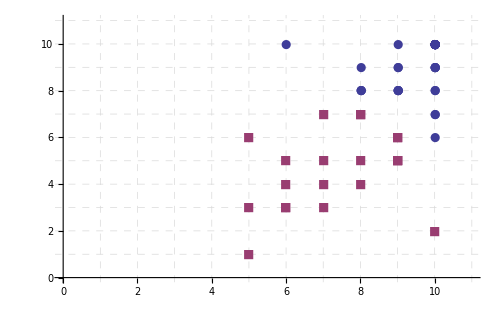

```mathematica
ListPlot[FindClusters[cc1], GridLines->{Range[11], Range[11]}, GridLinesStyle-> Directive[Dashed],PlotMarkers->{Automatic, 12}, PlotRange->{{0,11}, {0,11}},BaseStyle->{14, Bold, FontFamily->"Helvetica"}, ImageSize->500]
```

```mathematica
ManhattanDistance[dCEO, dCIO]
```

88.

```mathematica
dByAudience = Take[dByField, {4,13}]
```

{{10.,10.,10.,9.,10.,8.,10.,8.,10.,9.,10.,8.,10.,10.,9.,8.,9.,9.,5.,8.,5.,8.,8.,6.,6.,5.,6.,8.,6.,6.,6.,5.,8.,9.,8.,10.,4.,10.,10.,10.,10.,4.,9.,6.,6.,2.,6.,5.,4.,4.,3.,6.,9.,7.,3.,2.,4.,2.,1.,2.},{10.,10.,10.,10.,10.,9.,10.,9.,10.,9.,10.,9.,10.,10.,10.,10.,9.,10.,6.,10.,7.,9.,8.,8.,5.,6.,8.,8.,7.,7.,6.,8.,8.,8.,8.,10.,5.,10.,10.,10.,10.,5.,5.,5.,4.,2.,7.,7.,4.,6.,5.,8.,9.,10.,3.,3.,4.,3.,1.,3.},{10.,10.,10.,10.,10.,10.,10.,9.,10.,10.,10.,9.,10.,10.,9.,10.,9.,10.,9.,10.,8.,9.,9.,7.,6.,6.,8.,8.,8.,7.,7.,8.,10.,9.,8.,10.,5.,10.,10.,9.,10.,6.,7.,6.,6.,5.,7.,8.,4.,5.,5.,5.,8.,7.,3.,3.,5.,3.,1.,4.},{10.,10.,10.,10.,10.,10.,10.,9.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,9.,10.,10.,9.,10.,9.,8.,9.,9.,9.,8.,10.,10.,8.,10.,9.,8.,10.,9.,10.,10.,9.,10.,9.,7.,9.,8.,10.,7.,8.,7.,5.,6.,8.,8.,6.,7.,6.,6.,6.,5.,5.},{10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,9.,10.,10.,10.,10.,9.,10.,8.,10.,10.,9.,8.,9.,8.,10.,10.,10.,10.,7.,10.,8.,10.,10.,10.,10.,9.,8.,10.,9.,8.,9.,9.,9.,9.,8.,8.,7.,7.,8.},{10.,10.,10.,10.,10.,10.,10.,9.,9.,9.,10.,9.,10.,10.,10.,10.,10.,10.,10.,8.,10.,9.,8.,10.,9.,9.,8.,9.,9.,7.,8.,7.,9.,8.,8.,8.,8.,10.,10.,7.,8.,8.,9.,6.,7.,6.,6.,10.,4.,7.,8.,7.,10.,7.,9.,5.,8.,3.,7.,7.},{10.,10.,10.,10.,10.,9.,10.,9.,9.,9.,9.,9.,7.,7.,9.,8.,9.,7.,8.,8.,10.,9.,8.,6.,9.,9.,8.,8.,9.,8.,8.,10.,7.,5.,8.,5.,7.,7.,7.,8.,6.,7.,10.,10.,10.,5.,6.,7.,8.,7.,6.,6.,2.,6.,7.,8.,4.,5.,7.,7.},{10.,10.,10.,10.,9.,10.,8.,10.,8.,9.,8.,10.,6.,7.,9.,7.,7.,6.,9.,7.,10.,8.,7.,8.,9.,8.,5.,8.,9.,8.,8.,8.,5.,5.,10.,5.,9.,6.,5.,10.,4.,10.,5.,10.,9.,10.,6.,5.,10.,4.,5.,6.,1.,3.,3.,10.,4.,6.,7.,5.},{10.,10.,9.,8.,9.,8.,7.,10.,9.,8.,6.,8.,9.,8.,7.,7.,8.,10.,9.,7.,8.,8.,7.,9.,9.,9.,10.,6.,9.,9.,10.,8.,6.,9.,8.,4.,9.,4.,4.,5.,5.,8.,5.,7.,7.,8.,7.,4.,6.,8.,4.,4.,1.,4.,7.,5.,5.,8.,7.,4.},{10.,10.,10.,10.,10.,9.,10.,10.,10.,9.,10.,8.,10.,10.,8.,10.,10.,8.,10.,10.,7.,10.,10.,10.,10.,9.,10.,9.,8.,9.,7.,7.,9.,10.,6.,10.,9.,4.,4.,5.,6.,8.,10.,5.,4.,9.,6.,4.,5.,6.,10.,3.,8.,3.,5.,3.,6.,7.,6.,5.}}

```mathematica
md2= Table[ManhattanDistance[dByAudience[[i]], dByAudience[[j]]], {i, 1, Length[dByAudience]}, {j, 1, Length[dByAudience]}]
```

{{0.,50.,56.,116.,150.,106.,128.,157.,155.,129.},{50.,0.,36.,88.,120.,88.,122.,153.,149.,115.},{56.,36.,0.,62.,106.,72.,108.,141.,133.,99.},{116.,88.,62.,0.,48.,64.,96.,117.,115.,87.},{150.,120.,106.,48.,0.,66.,102.,139.,137.,101.},{106.,88.,72.,64.,66.,0.,84.,135.,119.,89.},{128.,122.,108.,96.,102.,84.,0.,73.,99.,117.},{157.,153.,141.,117.,139.,135.,73.,0.,90.,134.},{155.,149.,133.,115.,137.,119.,99.,90.,0.,96.},{129.,115.,99.,87.,101.,89.,117.,134.,96.,0.}}

NumberForm::sigz: In addition to the number of digits requested, one or more zeros will appear as placeholders.

General::stop: Further output of NumberForm :: sigz will be suppressed during this calculation.

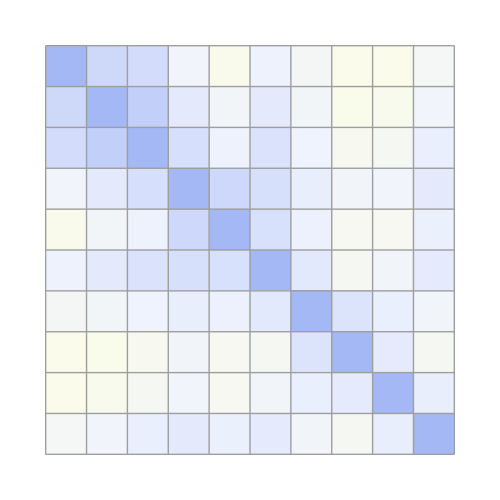
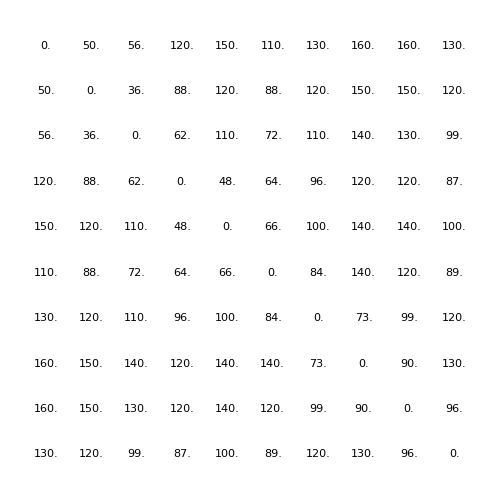
-Graphics-
-Graphics--Graphics--Graphics-

```mathematica
mdTable = Column[{GraphicsRow[audiences,ImageSize->500,Frame->All],Row[{GraphicsColumn[audiences,ImageSize->50,Frame->All],Overlay[{ArrayPlot[md2,ColorFunction->(ColorData["TemperatureMap"][(1+(#/160))/4]&),Frame->None,Mesh->True,PlotRangePadding->0,ImageSize->500,ColorFunctionScaling->False],GraphicsGrid[Map[NumberForm[#,2]&,md2,{2}],ImageSize->500]}]}]},Alignment->Right,Spacings->0]
```